```mathematica
(*plot in color*)
colors=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(*plot in grayscale*)
colors={RGBColor[0.3,0.3,0.3],RGBColor[0.4,0.4,0.4],RGBColor[0.6,0.6,0.6],RGBColor[0.1,0.1,0.1]}
```

{RGBColor[0.3, 0.3, 0.3],RGBColor[0.4, 0.4, 0.4],RGBColor[0.6, 0.6, 0.6],RGBColor[0.1, 0.1, 0.1]}

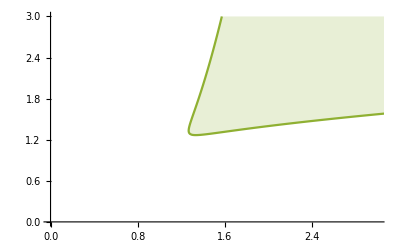

```mathematica
(*import cusp data points*)
SetDirectory[NotebookDirectory[]];
cusp=Import["Cusp.csv"];
cuspInterp=Import["Cusp_interp.mat","LabeledData"];
cuspBottom=cuspInterp[[1,2]];
cuspTop=cuspInterp[[2,2]];

cuspBottomLeft=cuspBottom[[1;;376]];
cuspBottomRight=cuspBottom[[376;;Length[cuspBottom]]];
cuspTopLeft=cuspTop[[1;;376]];
cuspTopRight=cuspTop[[376;;Length[cuspTop]]];

pcusp=ListPlot[cusp,Joined->True,PlotRange->{{0,3},{0,3}},PlotStyle->{colors[[3]]},Filling->Top]

(*set μ and define variables for bifurcation line*)
μ=0.03;
alphaRoot=Solve[-alpha+(6μ+2)/(1-6μ)==0,alpha][[1,1,2]];
lineTable=Table[{alpha,-alpha+(6μ+2)/(1-6μ)},{alpha,1.25,1.386,0.001}];

(*font sizes*)
fontTicks=18;
fontAxesLabel=24;
fontAnnotations=22;
```

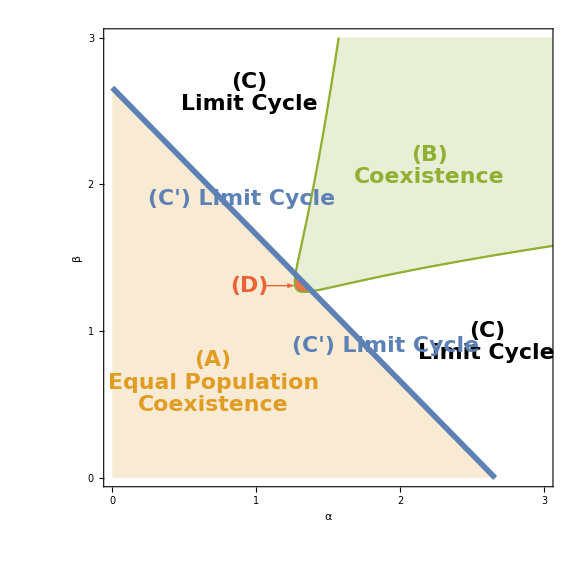

```mathematica
(*lines and shading*)
p1=Plot[-alpha+(6μ+2)/(1-6μ),{alpha,0,alphaRoot},PlotStyle->colors[[2]],Filling->Axis,PlotRange->{{0,3},{0,3}},ImageSize->Large,AspectRatio->1,Frame->{{True,False},{True,False}},FrameTicks->{{0,1,2,3},{0,1,2,3}},FrameTicksStyle->Directive[fontTicks,FontFamily->"Latin Modern Sans"],FrameLabel->{"α","β"},LabelStyle->Directive[fontAxesLabel,FontFamily->"Latin Modern Math"],RotateLabel->False];
p2=Plot[-alpha+(6μ+2)/(1-6μ),{alpha,0,alphaRoot},PlotStyle->{Thickness[0.007],colors[[1]]}];

pcuspcurve=ListPlot[cusp,Joined->True,PlotRange->{{0,3},{0,3}},PlotStyle->{Thick,colors[[3]]}];

regionDshade1=ListPlot[{cuspBottomRight,lineTable},Joined->True,FillingStyle->Directive[Opacity[0.85],colors[[4]]],PlotStyle->Thickness[0.0001],Filling->{1->{2}},PlotRange->All];
regionDshade2=ListPlot[{cuspBottomLeft,cuspTopLeft},Joined->True,FillingStyle->Directive[Opacity[0.85],colors[[4]]],PlotStyle->Thickness[0.0001],Filling->{2->{1}},PlotRange->All];

(*text annotations*)
t1a=Graphics[Text[Style["(A)",Bold,fontAnnotations,colors[[2]]],{0.7,0.8}]];
t1b=Graphics[Text[Style["Equal Population",Bold,fontAnnotations,colors[[2]]],{0.7,0.65}]];
t1c=Graphics[Text[Style["Coexistence",Bold,fontAnnotations,colors[[2]]],{0.7,0.5}]];
t2a=Graphics[Text[Style["(B)",Bold,fontAnnotations,colors[[3]]],{2.2,2.2}]];
t2b=Graphics[Text[Style["Coexistence",Bold,fontAnnotations,colors[[3]]],{2.2,2.05}]];
t3a=Graphics[Text[Style["(C)",Bold,fontAnnotations],{0.95,2.7}]];
t3b=Graphics[Text[Style["Limit Cycle",Bold,fontAnnotations],{0.95,2.55}]];
t4a=Graphics[Text[Style["(C)",Bold,fontAnnotations],{2.6,1}]];
t4b=Graphics[Text[Style["Limit Cycle",Bold,fontAnnotations],{2.6,0.85}]];
t5a=Graphics[Text[Style["(C') Limit Cycle",Bold,fontAnnotations,colors[[1]]],{1.9,0.9},Automatic,{1,-1}]];
t5b=Graphics[Text[Style["(C') Limit Cycle",Bold,fontAnnotations,colors[[1]]],{0.9,1.9},Automatic,{1,-1}]];
t6a=Graphics[Text[Style["(D)",Bold,fontAnnotations,colors[[4]]],{0.95,1.31}]];

arrowD=Graphics[{Thick,colors[[4]],Arrowheads[.04],Arrow[{{1.05,1.31},{1.26,1.31}}]}];

(*show all curves and annotations in a single figure*)
Show[p1,pcusp,regionDshade1,regionDshade2,pcuspcurve,p2,t1a,t1b,t1c,t2a,t2b,t3a,t3b,t4a,t4b,t5a,t5b,t6a,arrowD]
```